# Lagaris Problem 7: 2nd-Order Nonlinear PDE BVP with Mixed BC

Solving the PDE in Mathematica:

```mathematica
pde=D[ψ[x,y],{x,2}]+D[ψ[x,y],{y,2}]+ψ[x,y]D[ψ[x,y],y]==Sin[π x](2-π^2 y^2+2 y^3 Sin[π x])
```

ψ[x,y] ψ^(0,1)[x,y]+ψ^(0,2)[x,y]+ψ^(2,0)[x,y]==Sin[π x] (2-π^2 y^2+2 y^3 Sin[π x])

```mathematica
DSolve[{
pde,
ψ[0,y]==0,
ψ[1,y]==0,
ψ[x,0]==0,
ψ[x,1]==2Sin[π x]
},ψ[x,y],{x,y}]
```

DSolve[{ψ[x,y] ψ^(0,1)[x,y]+ψ^(0,2)[x,y]+ψ^(2,0)[x,y]==Sin[π x] (2-π^2 y^2+2 y^3 Sin[π x]),ψ[0,y]==0,ψ[1,y]==0,ψ[x,0]==0,ψ[x,1]==2 Sin[π x]},ψ[x,y],{x,y}]

```mathematica
ψa[x_,y_]:=y^2 Sin[π x]
```

```mathematica
FullSimplify[D[ψa[x,y],x]]
```

π y^2 Cos[π x]

```mathematica
dψadx[x_,y_]:=π y^2 Cos[π x]
```

```mathematica
FullSimplify[D[ψa[x,y],y]]
```

2 y Sin[π x]

```mathematica
dψady[x_,y_]:=2 y Sin[π x]
```

```mathematica
FullSimplify[D[ψa[x,y],{x,2}]]
```

-π^2 y^2 Sin[π x]

```mathematica
d2ψadx2[x_,y_]:=-π^2 y^2 Sin[π x]
```

```mathematica
FullSimplify[D[ψa[x,y],{x},{y}]]
```

2 π y Cos[π x]

```mathematica
d2ψadxdy[x_,y_]:=2 π y Cos[π x]
```

```mathematica
FullSimplify[D[ψa[x,y],{y},{x}]]
```

2 π y Cos[π x]

```mathematica
d2ψadydx[x_,y_]:=2 π y Cos[π x]
```

```mathematica
FullSimplify[D[ψa[x,y],{y,2}]]
```

2 Sin[π x]

```mathematica
d2ψady2[x_,y_]:=2 Sin[π x]
```

```mathematica
Plot3D[ψa[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution (compare to Lagaris (1998), Figure 8)"]
```

-Graphics3D-

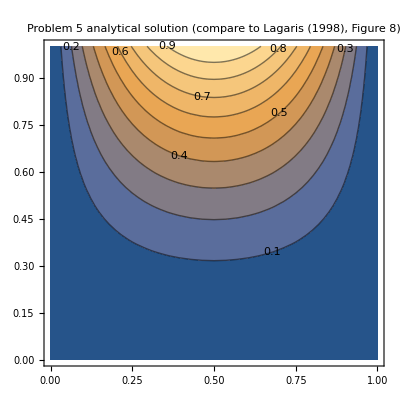

```mathematica
ContourPlot[ψa[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution (compare to Lagaris (1998), Figure 8)",ContourLabels->True]
```

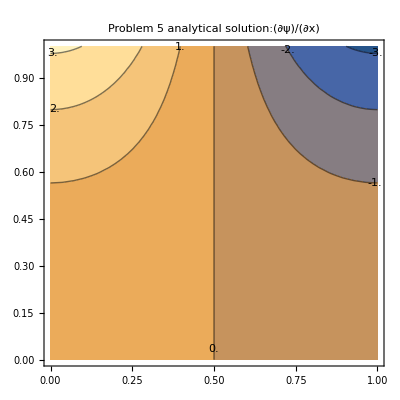

```mathematica
ContourPlot[dψadx[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(∂ψ)/(∂x)",ContourLabels->True]
```

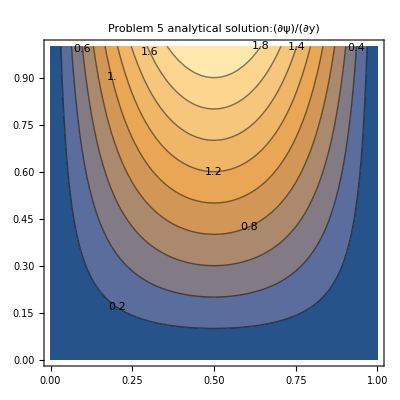

```mathematica
ContourPlot[dψady[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(∂ψ)/(∂y)",ContourLabels->True]
```

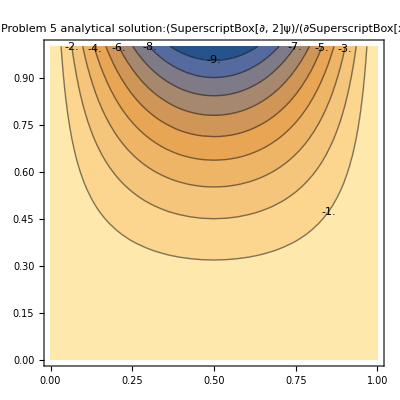

```mathematica
ContourPlot[d2ψadx2[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂SuperscriptBox[x, 2])",ContourLabels->True]
```

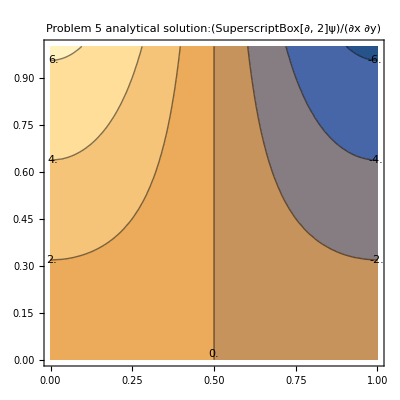

```mathematica
ContourPlot[d2ψadxdy[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂x ∂y)",ContourLabels->True]
```

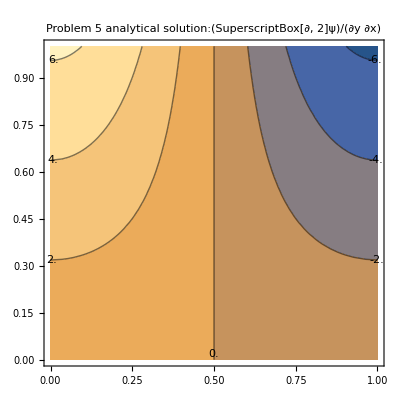

```mathematica
ContourPlot[d2ψadydx[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂y ∂x)",ContourLabels->True]
```

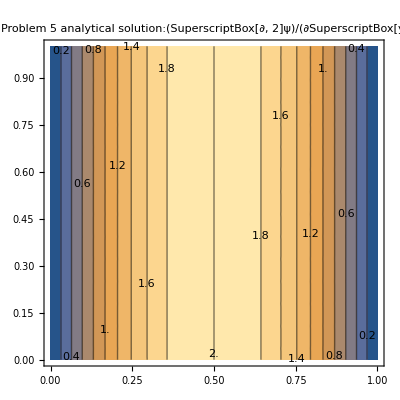

```mathematica
ContourPlot[d2ψady2[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂SuperscriptBox[y, 2])",ContourLabels->True]
```